```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes CAN

tmp

## temp

### Definition / Theorem

#### Example

Complex Integration

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
path[n_]:= Table[Exp[2*I*Pi*k/n], {k, 0, n}]

PlotPath[path_ , options___] :=
Module[{argand = Map[{Re[#], Im[#]}&, path]},grdata = {Line[argand],{PointSize[0.03],  Map[Point, argand]}};
Show[Graphics[grdata,AspectRatio -> 1,  Axes -> True, options]]]
```

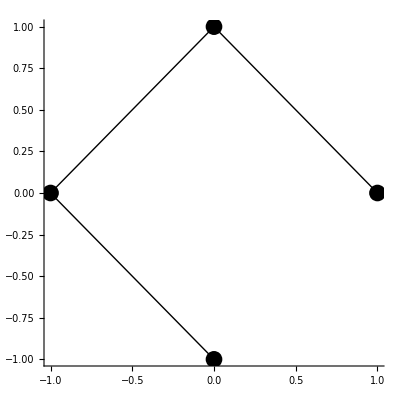

```mathematica
psp = {1, I, -1, -I};PlotPath[psp]
```

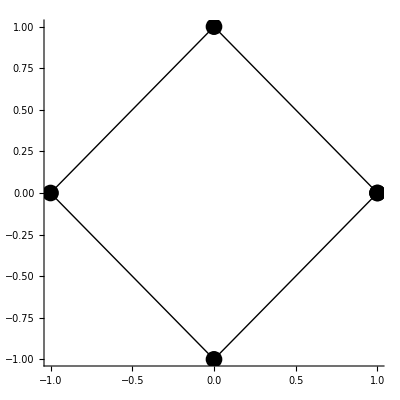

```mathematica
cpsp = {1, I, -1, -I, 1};PlotPath[cpsp]
```

```mathematica
ContourIntegral[expr_, vbl_, contour_] :=
	Integrate[expr, Prepend[contour, vbl]]
```

```mathematica
NContourIntegral[expr_, vbl_, contour_] :=
	NIntegrate[expr,Evaluate[ Prepend[contour, vbl]]]
```

```mathematica
ContourIntegral[1/z,z,cpsp]//Chop
```

2 ⅈ π

```mathematica
ContourIntegral[Sin[z]/z^2,z,cpsp]//Chop
```

2 ⅈ π

```mathematica
ContourIntegral[ⅇ^(-π z),z,{-ⅈ,ⅈ}]
```

0

```mathematica
ContourIntegral[(3z-1)^4,z,{2,2I+1/3 }]
```

-625/3+(2592 ⅈ)/5

```mathematica
ContourIntegral[z^2,z,{0,1+I}]//Expand
```

-2/3+(2 ⅈ)/3

```mathematica
ContourIntegral[1/z,z,-3/4-2/4I+path[12]]//Expand
```

2 ⅈ π

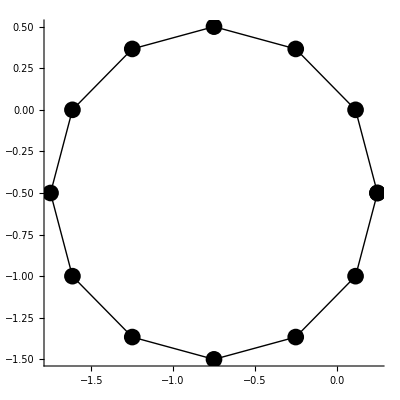

```mathematica
PlotPath[-3/4-2/4I+path[12]]
```

```mathematica
ClearAll[a,f,g]
f[z_]:=1/z
f[z_]:=(z^2+4)/(z-3)^3
g[t_]:=5 ⅇ^(2π ⅈ t)
Integrate[f[g[t]]g'[t],{t,0,1}]
Integrate[Abs[g'[t]],{t,0,1}]
```

2 ⅈ π

10 π

```mathematica
ContourIntegral[Conjugate[z],z,path[6]]//Expand
```

3 ⅈ √3

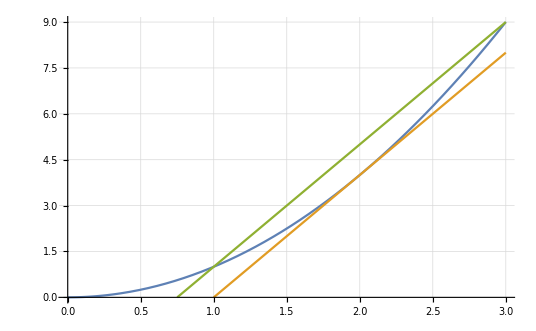

```mathematica
Plot[{x^2,4x-4,4x-3},{x,0,3},PlotRange->{0,9},GridLines->Automatic]
```

```mathematica
f[z_]:=(z^2+4)/(z-1)
f[x+I y]
ComplexExpand[f[x+I y]]
```

(4+(x+ⅈ y)^2)/(-1+x+ⅈ y)

-4/((-1+x)^2+y^2)+(4 x)/((-1+x)^2+y^2)-x^2/((-1+x)^2+y^2)+x^3/((-1+x)^2+y^2)+y^2/((-1+x)^2+y^2)+(x y^2)/((-1+x)^2+y^2)+ⅈ (-(4 y)/((-1+x)^2+y^2)-(2 x y)/((-1+x)^2+y^2)+(x^2 y)/((-1+x)^2+y^2)+y^3/((-1+x)^2+y^2))

```mathematica
u[x_,y_]:=-4/((-1+x)^2+y^2)+(4 x)/((-1+x)^2+y^2)-x^2/((-1+x)^2+y^2)+x^3/((-1+x)^2+y^2)+y^2/((-1+x)^2+y^2)+(x y^2)/((-1+x)^2+y^2)
v[x_,y_]:=-(4 y)/((-1+x)^2+y^2)-(2 x y)/((-1+x)^2+y^2)+(x^2 y)/((-1+x)^2+y^2)+y^3/((-1+x)^2+y^2)
```

```mathematica
D[u[x,y],{x,1}]//FullSimplify
D[v[x,y],{y,1}]//FullSimplify
```

1-(10 (-1+x)^2)/(((-1+x)^2+y^2)^2)+5/((-1+x)^2+y^2)

1-(10 (-1+x)^2)/(((-1+x)^2+y^2)^2)+5/((-1+x)^2+y^2)

```mathematica
D[u[x,y],{y,1}]//FullSimplify
-D[v[x,y],{x,1}]//FullSimplify
```

-(10 (-1+x) y)/(((-1+x)^2+y^2)^2)

-(10 (-1+x) y)/(((-1+x)^2+y^2)^2)

```mathematica
u[x,y]//FullSimplify
```

1+x+(5 (-1+x))/((-1+x)^2+y^2)

```mathematica
1/(2Pi ⅈ)ContourIntegral[z^3/(z-1/2I)^2,z,path[12]]
3 (1/2 I)^2
```

-3/4

-3/4

```mathematica
Simplify[%]
```

-(ⅈ π)/(4 ℼⅈ)

```mathematica
-(ⅈ π)/(4 ℼⅈ)
```

-(ⅈ π)/(4 ℼⅈ)

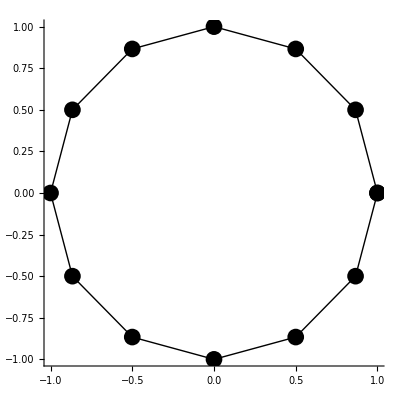

```mathematica
PlotPath[path[12]]
```

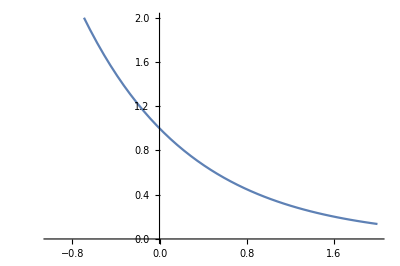

```mathematica
Plot[{ⅇ^-x,-ⅇ^-x},{x,-1,2},AxesOrigin->{0,0},AspectRatio->Automatic,PlotRange->{0,2}]
```

```mathematica
Gamma'[z]
```

Gamma[z] PolyGamma[0,z]

```mathematica
ClearAll[g]
g[s_]:=Integrate[x^(s-1)Exp[-x],{x,0,Infinity}]
g1[s_]:=Integrate[x^(s-1)Exp[-x] Log[x],{x,0,Infinity}]
```

```mathematica
Gamma'[4]//N
g1[4]//N
```

7.53671

7.53671

```mathematica
Gamma[1/2]
Gamma[3/2]
Gamma[5/2]
```

√π

(√π)/2

(3 √π)/4

```mathematica
ⅇ//N
```

2.71828

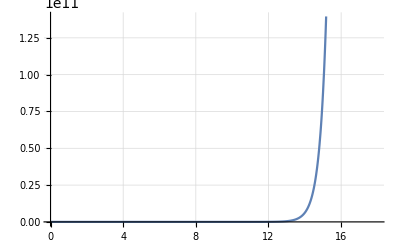

```mathematica
Plot[Gamma[x],{x,0,18},AxesOrigin->{0,0},GridLines->Automatic]
```

```mathematica
Gamma[0.5]
Gamma[2.8651495999]
```

1.77245

1.77245

```mathematica
Sin[π/2]
```

1

```mathematica
Sin[π/4]
```

1/(√2)

```mathematica
ComplexPlot3D[z Sin[1/z],{z,-4-4I,4+4I},ColorFunction->"CyclicLogAbsArg"]
```

-Graphics3D-

```mathematica
(π^(3/2)r^3)/Gamma[5/2]
```

(4 π r^3)/3

z-z^3/6+z^5/120-z^7/5040+z^9/362880+O[z]^10

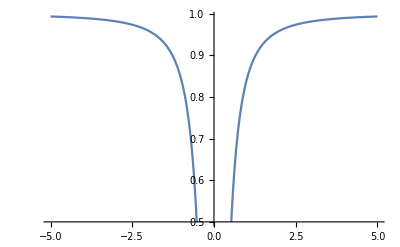

```mathematica
Series[Sin[z],{z,0,9}]
Plot[z Sin[1/z],{z,-5,5}]
```

```mathematica
x^(z-1)/(ⅇ^x-1)/.x:> r ⅇ^(π ⅈ)//FullSimplify
```

(-r)^(-1+z)/(-1+ⅇ^-r)

```mathematica
D[r ⅇ^(π ⅈ),{r,1}]
```

-1

```mathematica
ContourIntegral[(ⅇ^z-1)/z^4,z,path[8]]
2π ⅈ/6
```

(ⅈ π)/3

(ⅈ π)/3

```mathematica
Residue[(ⅇ^z-1)/z^4,{z,0}]
```

1/6

```mathematica
ClearAll[x]
Residue[x^8/(ⅇ^x-1),{x,0}]
ⅇ^(-π ⅈ)//N
```

0

-1.

```mathematica
Series[Cosh[1/z],{z,Infinity,5}]
```

1+1/(2 z^2)+1/(24 z^4)+O[1/z]^6